```mathematica
ClearAll["Global`*"]
```

```mathematica
data = Import[StringJoin[{$HomeDirectory,"/Dropbox/PostDoc/2014_DiffusingForager/DiffusingForager/mathematica/NewRateFigures_Final/densitydata.csv"}],"csv"];
carnivoredata = Import[StringJoin[{$HomeDirectory,"/Dropbox/PostDoc/2021_TaranWebs/carnivoredensities_trimmed.csv"}],"csv"];
```

```mathematica
LinearModelFit[Log@data,x,x]
```

FittedModel[-4.45983-0.776818 x]

```mathematica
eqnC = ((λ)/(0.5*(k)))*R*C-( σ*(1-R/(k))+μ+bP)*C/.{k->kRes,λ->λ[M],Y->Y[M],μ->μ[M],ρ->ρ[M],σ->σ[M],bP->bP[M](**PredPresence*)};(*take σ*(1-R/k)=0 to take out starvation component*)
eqnR = α*R*(1-R/(0.5*k))-(((λ)/(Y))*(R/(1*(k)))+ρ)*C/.{k->kRes,λ->λ[M],Y->Y[M],μ->μ[M],ρ->ρ[M],σ->σ[M],bP->bP[M](**PredPresence*)};
LVSS = FullSimplify[Solve[{0==eqnC,0==eqnR},{C,R}]];
Csol = C/.LVSS[[3]]
Rsol = R/.LVSS[[3]]
```

-(kRes α Y[M] (bP[M]-λ[M]+μ[M]) (bP[M]+μ[M]+σ[M]))/((λ[M]+σ[M]) (λ[M] (bP[M]+μ[M]+Y[M] ρ[M])+(λ[M]+Y[M] ρ[M]) σ[M]))

(kRes (bP[M]+μ[M]+σ[M]))/(λ[M]+σ[M])

Reproductive energetics for a mammalian carnivore

```mathematica
η=3/4;
(*B0=4.7*10^(-2);(*W g^−0.75*)*)
B0Pred =(10^0.32)(*kJ/day*)*((0.01157(*Watts*))/(1(*kJ/day*))); (* in (kJ/d) for carnivora from https://doi.org/10.1086/432852 USING LOG10!!!!! *)
EmPred=5774;(*Energy to synthesize a unit of biomass not during starvation J/gram*)

aPred = B0Pred/EmPred;
m0Pred[Mp_]:=0.097*Mp^0.92;
ϵLam = 0.95;
τLamPred[Mp_]:= -Log[(1-ϵLam^(1/4))/(1 - (m0Pred[Mp]/Mp)^(1/4))]*(4*Mp^(1/4))/aPred;
λPred[Mp_]:=(Log[2]/τLamPred[Mp]) (*Fecundity = 2*)
```

```mathematica
(*B0=4.7*10^(-2);(*W g^−0.75*)*)
(*E'=2*7000; (*J/g*)
a'=B0/E';*)
(*m[t_,Mp_]:=Mp*E^(-a*t/(Mp^(1-η)));Bpred[Mp_]:=Integrate[B0*m[t,Mp]^(η),{t,0,τLamPred[Mp]}]*)
Bpred[Mp_]:=Integrate[(((1-(1-(m0Pred[Mp]/Mp)^(1/4))*E^(-aPred*t/(4*Mp^(1/4)))))^4)*Mp,{t,0,τLamPred[Mp]}]
```

Predator individuals per area seems suspect because intercept should be *much less* than prey individuals per area... right now predator intercept is 72% of prey intercept...

From Mathias:
b0=2.51,b1=0.79,and b2=−0.37 using the raw values (which makes more sense)
In the PRSB paper I sampled values from the ranges of MLEs computed for the three regions (with no log transformation):b0=1.6332+(3.4895-1.6332)*rand(1);
b1=0.2109+(0.7912-0.2109)*rand(1);
b2=-0.3731+(-0.3045-(-0.3731))*rand(1);

```mathematica
PredsperArea[Mp_] :=(0.000862119)*Mp^-0.88; (*Inds/m^2 w/ Mp (grams) From Carbone and Gittleman, Science 2002*)
PredDensity[Mp_] := Mp*PredsperArea[Mp]; (*grams/ind * inds/meter^2 = grams/m^2*)
(*Parameterizations of the Rohr Model*)

palpha = 1.6332;
pbeta = 0.2109;
pgamma = -0.3731;
(*p = Exp[linkalpha + linkbeta*Log[M/Mp] + linkgamma*Log[M/Mp]^2];
prob = p/(1+p);
OptMass =M/.Solve[ D[prob,M]==0,M][[1]];*)
(*Optimal Prey mass given Predator (Mp) Mass*)
OptPreyMass[Mp_] :=ⅇ^(-pbeta/(2 pgamma)) Mp;
(*Optimal Predator mass given Prey (M) Mass*)
OptPredMass[M_]:=ⅇ^(pbeta/(2 pgamma)) M;
OptPreypermeter2[Mp_] := 0.1156*OptPreyMass[Mp]^-0.77;
(*Damuth: Average Individuals/m2*)
OptPreygramspermeter2[Mp_] :=OptPreypermeter2[Mp]*OptPreyMass[Mp] ;
(*Average Individuals/m2 * average grams/individual*)
(*Percent fat + muscle*)
(*percentconsumable[M_]:=( 0.02*M^1.19 + 0.38*M^1.00)/M;*)
(*Or 1 - percent skeletal*)
massSkeletalgrams[M_]:= 0.0335*M^1.09263;
massFatgrams[M_]:=0.02*M^1.19;
massMusclegrams[M_]:=0.38*M^1.0;
massOthergrams[M_]:=M-(massSkeletalgrams[M]+massFatgrams[M]+massMusclegrams[M]);
(*This is nearly 100% from Prange et al. AmNat 1979*)
(*Energy Density of PREY Joules/gram*)
(*BLUBBER energy content 37670 J/gram SAME AS FAT *)
(*NOTE: THINK CAREFULLY ABOUT THIS *)
FatJperG = 37700;
ProteinJperG = 17900;
MuscleJperG = 0.4*ProteinJperG + 0.6*FatJperG;
(*TissueJperG = ProteinJperG+FatJperG;
PercentFat =(FatJperG/TissueJperG);
PercentProtein =(1- PercentFat);*)
Eprey[M_]:=(1/(M))*(massFatgrams[M]*FatJperG+massMusclegrams[M]*MuscleJperG+massOthergrams[M]*MuscleJperG);
(*Eprey[M_,ϵEprey_] := ((PercentProtein*TissueJperG)+(PercentFat*TissueJperG)+0)*(1+ϵEprey)*percentconsumable[M];*)
(*Joules/gram: 17000 protein + 37000 fat + 0 carb per gram of meat http://www.fao.org/3/y5022e/y5022e04.htm  Modified from Merrill and Watt (1973).*)
(*Results of MAXSIZE are very sensitive to Energy Density of Prey*)
(*Yield of predator per prey*)
Ypred[Mp_,M_] := (Mp*Eprey[M])/Bpred[Mp]; (*Grams of predator per grams of prey*)
kprey[Mp_]:=OptPreygramspermeter2[Mp]; (*PREY carrying capacity grams/m^2*)
```

Okay... this needs to be checked with Chris... here is the idea:
We can’t really specify at what Herbivore density Predator growth is maximized... but we can say that Predator growth scales with Herbivore growth, and that Herbivore growth is maximized when the Resources are 1/2 Resource Carrying Capacity.
So given a Resource Carrying Capacity (23000 g/m^2), we use the Prey Yield Equation = Grams of Prey / Grams of Resource, to calculate Prey density where prey growth is maximized ->  
PreyYield * Resource Carrying Capacity * (1/2) = (grams prey / grams resource) * grams resource / m^2 = grams prey / m^2

```mathematica
MuscleJperG
```

29780.

```mathematica
FullSimplify[massOthergrams[M]]
```

M-0.38 M^1.-0.0335 M^1.09263-0.02 M^1.19

```mathematica
Ed=18200; (*J/g of plant Resource *)
B0=4.7*10^(-2);(*W g^−0.75 for herbivores*)
Em=5774;(*J/gram - energy required to build gram of herbivore*)
a = B0/Em;
τLam[M_]:= -Log[(1-ϵLam^(1/4))/(1 - (m0[M]/M)^(1/4))]*(4*M^(1/4))/a;
λ[M_]:=(Log[2]/τLam[M]) (*Fecundity = 2*) (* max consumer growth rate of herbivore *)
BLam[M_]:=1/(3 a)ⅇ^(-(a τLam[M])/M^(1/4)) M^(1/4) (3 (-1+ⅇ^((a τLam[M])/M^(1/4))) m0[M]+M (-48 ⅇ^((3 a τLam[M])/(4 M^(1/4))) (-1+(m0[M]/M)^(1/4))-36 ⅇ^((a τLam[M])/(2 M^(1/4))) (-1+(m0[M]/M)^(1/4))^2-16 ⅇ^((a τLam[M])/(4 M^(1/4))) (-1+(m0[M]/M)^(1/4))^3+3 (-1+4 (m0[M]/M)^(1/4)-6 √(m0[M]/M)+4 (m0[M]/M)^(3/4))+ⅇ^((a τLam[M])/M^(1/4)) (-25+12 (m0[M]/M)^(1/4)+6 √(m0[M]/M)+4 (m0[M]/M)^(3/4)))+3 a ⅇ^((a τLam[M])/M^(1/4)) M^(3/4) τLam[M]);
m0[M_]:=0.097*M^0.92;
kRes=23000;(*grams/m^2 carrying capacity of resource*)
YHerbperRes[M_]:=M*Ed/BLam[M]; (*Grams herb / Grams Resource given the mass of an Herbivore*)
```

Here we calculate the PREY DENSITY that MAXIMIZES PREDATOR GROWTH
Because predator growth follow prey growth, which follows resource growth, we don’t actually know at what point predator growth is maximized apriori
Our current solution, then, is to calculate the prey density where prey growth is maximized and to convert that into predator biomass.
Prey growth is maximized when resource growth -- which grows logistically -- is at 1/2 resource carrying capacity K_r.

So (1/2)*(Yield :: grams herbivore / grams grass)* K_r = grams of herbivore when resource has maximum growth

```mathematica
PreyDensityMaxResourceGrowth[Mp_] := YHerbperRes[OptPreyMass[Mp]]*(1/2)*kRes; (*Grams Herb / m^2 given the mass of a predator and the optimal prey mass given predator mass conversion*)
```

Let’s look at what Prey Density under Max Resource Growth looks like compared to steady state data. Predicted steady states are high bc. growth is maximized.
I THINK THIS DOES A PRETTY GOOD JOB OF CATCHING OBSERVED MAX DENSITY, which we can interpret as the data region capturing max growth.

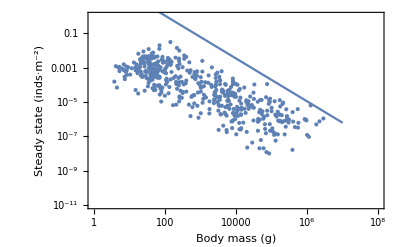

```mathematica
Show[{
ListLogLogPlot[data,PlotRange->{{1,10^8},{10^-11,1}},Frame->True,FrameLabel->{"Body mass (g)","Steady state (inds·m^-2)"},PlotRange->{10^-11,10^5}],
LogLogPlot[(1/M)*PreyDensityMaxResourceGrowth[M],{M,1,10^7},Frame->True]
}]
```

From the prey density where prey growth is maximized, we convert that to predator density
This gives us: 
The predator density where predator growth is maximized, assuming predator growth is maximized where prey growth is maximized where resource growth is maximized

```mathematica
PredDensityMaxPreyGrowth[Mp_,M_,ϵEprey_] :=Evaluate[Ypred[Mp,M]* (PreyDensityMaxResourceGrowth[Mp]*(1+ϵEprey))//Simplify];(*gpred/gprey * gprey/m^2 = gpred/m^2*)
```

Let’s look at what Maximal Density PREDATOR Growth looks like compared to steady state data. Predicted steady states are high bc. growth is maximized.
Predator densities at maximal predator growth always less than prey maximal densities... hard to compare to data because data is for all mammals

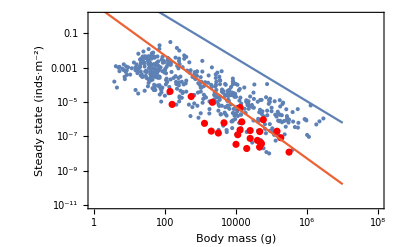

```mathematica
Show[{
ListLogLogPlot[data,PlotRange->{{1,10^8},{10^-11,1}},Frame->True,FrameLabel->{"Body mass (g)","Steady state (inds·m^-2)"},PlotRange->{10^-11,10^5}],
ListLogLogPlot[carnivoredata,PlotStyle->Red],
LogLogPlot[(1/M)*PreyDensityMaxResourceGrowth[M],{M,1,10^7},Frame->True],
LogLogPlot[(1/M)*PredDensityMaxPreyGrowth[OptPredMass[M],M,0],{M,1,10^7},Frame->True,PlotStyle->ColorData[97,4]]
}]
```

```mathematica
predrate[Mp_,M_,ϵEprey_] := (λPred[Mp]*PredDensity[Mp])/PredDensityMaxPreyGrowth[Mp,M,ϵEprey](*((1/time)*gpred/m^2)/(gpred/m^2)=1/time*)
```

```mathematica
Ypredexpanded = Ypred[Mp,M,ϵEprey];
predrateexpanded = FullSimplify[predrate[Mp,M,ϵEprey]];
```

This line (below) allows faster implementation/plotting of the predrate function!

```mathematica
predratefull[Mp_,M_,ϵEprey_]:=  Evaluate[predrateexpanded//Simplify]
```

Now plot Herbivore-centric rates...
We want to compare the reproduction rate of the herbivore population to the predation rate from the implicit predator population

Now we compare the rates... where they cross implies change in dynamics

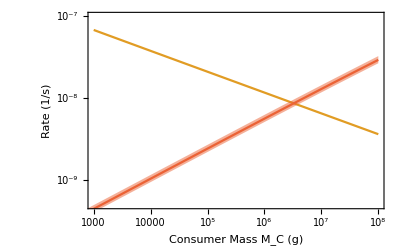

```mathematica
MortRateComparisonPlot = 
Show[{
LogLogPlot[
λ[M],{M,1000,1*10^8},Frame->True,FrameLabel->{"Consumer Mass M_C (g)","Rate (1/s)"},ImageSize->300,PlotStyle->ColorData[97,2],PlotRange->{5*10^-10,10^-7},LabelStyle->Directive[FontSize->14]],
LogLogPlot[{predratefull[OptPredMass[M],M,0],predratefull[OptPredMass[M],M,-0.1],predratefull[OptPredMass[M],M,0.1]},{M,1,1*10^8},PlotStyle->{ColorData[97,4],Transparent,Transparent},Filling->{2->{3}},FillingStyle->Directive[ColorData[97,4],Opacity[0.5]]]
},ImageSize->400]
```

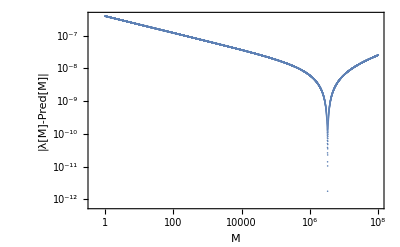

3.27341×10^6

2467.48

```mathematica
RepMinusPred =ParallelTable[{10^i,Abs[λ[10^i]-predratefull[OptPredMass[10^i],10^i,0]]},{i,0,8,0.001}];
ListLogLogPlot[RepMinusPred,Frame->True,FrameLabel->{"M","|λ[M]-Pred[M]|"}]
MaxPreyMass=RepMinusPred[[Position[RepMinusPred,Min[RepMinusPred]][[1]][[1]]]][[1]]
MaxPredMass=OptPredMass[MaxPreyMass]/1000
```

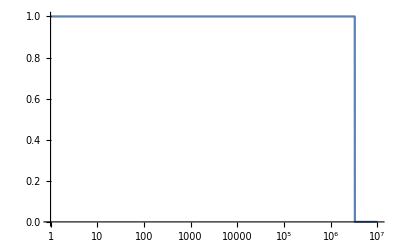

```mathematica
PredPresence = HeavisideTheta[MaxPreyMass-M];
LogLinearPlot[PredPresence,{M,1,10^7}]
```

```mathematica
(* Parameters that go into the model *)
(* Those that rely on mass have been made into functions for better exploration *)

s=1;
Emprime =7000;
aprime =  B0/Emprime;
γ=1.19;
ζ=1.00;
f0=0.0202;
mm0=0.383;
α=(*2.10*10^(-9)*)(9.45*10^(-9));
(*k=(*10*)23000/2;*)
ρ[M_]:=B0*M^(η)/(M*Ed);
a0 = 1.88*10^-8 ;(*sec grams^-b0*)
a1=1.45*10^-7;
a2=4.04*10^6;
b0=-0.56;
b1=-0.27;
b2=0.30;
μ[M_] := (a0*(Exp[a1*a2*M^(b1+b2)]-1)*M^(b0-b1-b2))/(a1*a2)   (* this is the consumer death rate*)
(*STARVATION MORTALITY*)
ϵsig[M_] := (1-(f0*M^γ+mm0*M^ζ)/M);(*mortality from starvation state*)
τsig [M_]:=-M^(1/4)/aprime*Log[ϵsig[M]];(*time it takes to go from full to dead*)
σ[M_] := 1/τsig [M];(*starvation mortality rate)*)

bP[M_] :=predratefull[OptPredMass[M],M,0];
Y[M_]:=YHerbperRes[M];
```

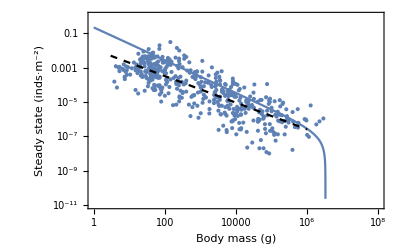

```mathematica
PredationDamuthPlot = Show[{
ListLogLogPlot[data,PlotRange->{{1,10^8},{10^-11,1}},Frame->True,FrameLabel->{"Body mass (g)","Steady state (inds·m^-2)"},PlotRange->{10^-11,10^5},LabelStyle->Directive[FontSize->14]],
LogLogPlot[(1/M)*Csol,{M,1,1*10^8},Frame->True],
LogLogPlot[Exp[-4.459834805724913]*x^-0.7768181657741381,{x,3,10^6},PlotStyle->Directive[Black,Dashed]]
},ImageSize->400]
```

```mathematica
MinimumObservedDensity = Min[data[[All,2]]]
MaximumObservedMass = Max[data[[All,1]]]
```

1.×10^-8

2860000

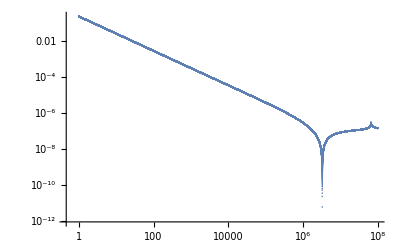

```mathematica
ListDensity =Abs[ParallelTable[{10^i,(1/M)*Csol/.M->10^i},{i,0,8,0.0001}]];
ListLogLogPlot[ListDensity]
```

```mathematica
MaxPreyMassSS=ListDensity[[Position[ListDensity,Min[ListDensity]][[1]][[1]]]][[1]]
```

3.27265×10^6

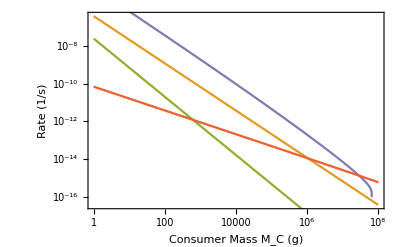

```mathematica
MortRateComparisonPlotPerMass= 
Show[{
LogLogPlot[
(1/M)*λ[M],{M,1,1*10^8},Frame->True,FrameLabel->{"Consumer Mass M_C (g)","Rate (1/s)"},ImageSize->300,PlotStyle->ColorData[97,2],PlotRange->Automatic,(*{5*10^-10,10^-7}*)LabelStyle->Directive[FontSize->14]],
LogLogPlot[
(1/M)*σ[M],{M,1,1*10^8},PlotStyle->ColorData[97,5]],
LogLogPlot[
(1/M)*μ[M],{M,1,1*10^8},PlotStyle->ColorData[97,3]],
LogLogPlot[{(1/M)*predratefull[OptPredMass[M],M,0],(1/M)*predratefull[OptPredMass[M],M,-0.1],(1/M)*predratefull[OptPredMass[M],M,0.1]},{M,1,1*10^8},PlotStyle->{ColorData[97,4],Transparent,Transparent},Filling->{2->{3}},FillingStyle->Directive[ColorData[97,4],Opacity[0.5]]]
},ImageSize->400]
```

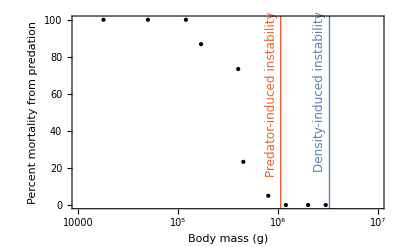

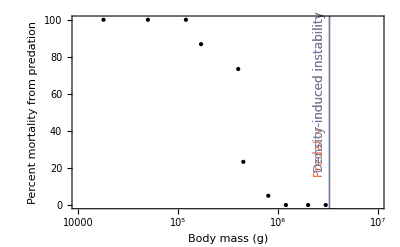

```mathematica
SinclairHerbMass = {3000,2000,1200,800,450,400,170,120,50,18}*1000;
SinclairHerbPercMort = {0,0,0,5,23.3,73.4,86.8,100,100,100};
SinclairPlot = Show[{
ListLogLinearPlot[Transpose[{SinclairHerbMass,SinclairHerbPercMort}],Frame->True,PlotRange->{{10000,10^7},All},PlotStyle->Directive[Black,PointSize[Large]],FrameLabel->{"Body mass (g)","Percent mortality from predation"},LabelStyle->Directive[FontSize->14]],
Graphics[{Thick,ColorData[97,4],Line[{{Log@MaxPreyMass,-10},{Log@MaxPreyMass,110}}]}],
Graphics[{Thick,ColorData[97,1],Line[{{Log@MaxPreyMassSS,-10},{Log@MaxPreyMassSS,110}}]}],
Graphics[Text[Style["Predator-induced instability",FontSize->12,ColorData[97,4]],{Log@MaxPreyMass*(1-0.015),60},Automatic,{0,100}]],
Graphics[Text[Style["Density-induced instability",FontSize->12,ColorData[97,1]],{Log@MaxPreyMassSS*(1-0.015),61},Automatic,{0,100}]]
},ImageSize->400]
```

```mathematica
Table[ColorData[97,i],{i,1,6}]
```

{RGBColor[0.368417, 0.506779, 0.709798],RGBColor[0.880722, 0.611041, 0.142051],RGBColor[0.560181, 0.691569, 0.194885],RGBColor[0.922526, 0.385626, 0.209179],RGBColor[0.528488, 0.470624, 0.701351],RGBColor[0.772079, 0.431554, 0.102387]}

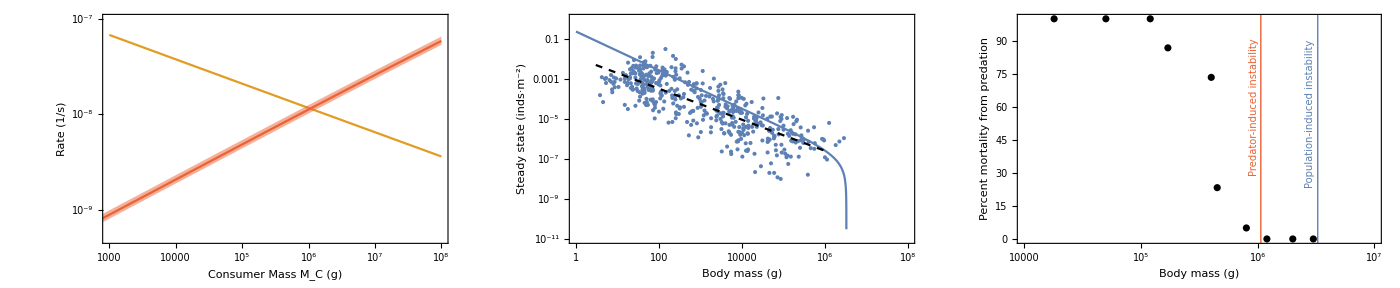

```mathematica
PredPlot = GraphicsGrid[{{MortRateComparisonPlot,PredationDamuthPlot,SinclairPlot}},ImageSize->1400,Spacings->Scaled[0]]
```

```mathematica
Export[StringJoin[{$HomeDirectory,"/Dropbox/PostDoc/2021_TaranWebs/figures/fig_predationrate.pdf"}],PredPlot,"PDF"]
```

/Users/jdyeakel/Dropbox/PostDoc/2021_TaranWebs/figures/fig_predationrate.pdf